# Pieces of Art Appreciated with Wolfram Language Machine Learning

Applying machine learning and the Wolfram Language functionality to learn about five of the most famous painting artist in history.

Diego Gutierrez Coronel, Jun. 28,  2018

Mathematica and the Wolfram Language is known for being a symbolic language that also works well for plotting and visualisation. However it can be used for much more, with a simple but broad functionality for Machine Learning. It can be very useful to analyze data, simulate processes, either scientific or mathematical, and even develop software for different applications. Art appreciation and categorization can be though of as a subjective topic not related with computation. However, nowadays the tools developed by machine learning have already been used to study art history, style, among others.

## From Renaissance to Post-Impressionism

We will apply some of the Machine Learning tools in the Wolfram Language to look at five different artist as shown in the list created below. Each one of the artists belonging to different periods of time and stylistic movements in art. Representing the Italian Renaissance is Sandro Botticelli, form the Baroque period is Spanish artist Diego Velázquez, and his famous compatriot Pablo Picasso, figure of the Cubistic style. Additionally we have Claude Monet and Vincent van Gogh from opposing movements, Impressionism and Post-Impressionism, respectively. With the Wolfram Language, this set of strings can be converted into real-world entities that can be used symbolically.

```mathematica
paintersList = {"Sandro Boticelli", "Diego Velazquez", "Claude Monet", "Vincent Van Gogh", "Picasso"};
Interpreter["Person"][#] & /@ paintersList
colors={Blue,Red,Green,Gray,Orange};
```

{Sandro Botticelli,Diego Velázquez,Claude Monet,Vincent van Gogh,Pablo Picasso}

These entities contain different properties and thus we can access information and various types of data from this symbolic expressions. Here we take a random sample of three famous paintings from Botticelli. We can also check the number of “Notable Artworks” Images stored under Botticelli’s Entity.

```mathematica
EntityValue[RandomSample[LinguisticAssistant["NotableArtworks"], 3], "Image"]
Length[Cases[EntityValue[EntityList[LinguisticAssistant["NotableArtworks"]],"Image"],_Image]]
```

{-Graphics-,-Graphics-,-Graphics-}

52

With the following code we assign a list of 5 lists of notable paintings from each of the artists presented.

```mathematica
paintingImages=Cases[EntityValue[
RandomSample[Interpreter["Person"][#]["NotableArtworks"], 40],"Image"],_Image]&/@paintersList;
```

We can also see the total number of paintings stored below and a sample of these.

```mathematica
Length[Flatten[paintingImages]]
paintingImages⟦4,9⟧
```

178

-Graphics-

## Color Appreciation

These paintings could be analyzed in different ways. We could for example see the distinctive colors used by each artist by taking the pixel color of all images for each of the artist and plotting it in a Chromaticity Plot.

```mathematica
Legended[Show[
		ChromaticityPlot[#1,PlotStyle->#2,]&@@@Transpose[{paintingImages,colors}]
		],SwatchLegend[colors,paintersList]]
```

-Graphics-

This same data set can be visualized thoroughly and interactively by plotting it in three dimensions. The description box in light blue is just a set of options for plotting so do not focus too much on those.

```mathematica
Legended[
Show[Table[ChromaticityPlot3D[paintingImages[[i]],PlotStyle->colors[[i]],],{i,1,5}]],
SwatchLegend[colors,paintersList]]
```

-Graphics3D-

It can be seen that the colors used by all artist are clustered in a relatively small range, however each one of them seems to disperse in different directions in the cluster. For instance Van Gogh does not use so many light colors as Monet or Picasso.

## Introduction Machine Learning

For now we will generate a list of rules that connects painters with their paintings as seen in a random sample below.

```mathematica
dataset=Thread/@Thread[paintingImages->paintersList];
dataset=RandomSample[Flatten[dataset]];
RandomSample[dataset,5]
```

{-Graphics-→Diego Velazquez,-Graphics-→Claude Monet,-Graphics-→Sandro Boticelli,-Graphics-→Vincent Van Gogh,-Graphics-→Sandro Boticelli}

Now we will look at different two paradigms in machine learning implemented in Wolfram Language Functions. These are supervised and unsupervised learning. In a general and conceptual way:

Supervised learning: takes a relation between inputs and outputs.

Unsupervised learning: takes only outputs and finds patterns or clusters.

We separate the total number of paintings in a training set and a test set in order to work with built-in functions. The training set can be small to actually obtain accurate results with the machine learning algorithms. However, we will focus more on this as a demonstration and an introduction to machine learning in Mathematica.

```mathematica
Length[dataset]
trainingset=dataset[[1;;140]];
testset=dataset[[141;;]];
```

178

## Classifying by Artist

Below we use the built-in function Classify to generate a classifier function using the training set defined before. This employs the best model to be able to classify paintings with an intrinsic probability, and some general features useful for testing it. It can be seen, that by clicking in the plus sign of the description the classifier function used either a Logistic Regression or Nearest Neighbors method. It is worth noting that the Classify function has multiple options to select an appropriate algorithm for the task needed.

```mathematica
cfunction=Classify[trainingset]
```

ClassifierFunction[…]

Now the classifier function is used on a test set, and then see the interesting and quantitative results from the test.

```mathematica
cmeasurements=ClassifierMeasurements[cfunction,testset]
```

ClassifierMeasurementsObject[…]

With the following it can be seen how accurate is the classifier function. Also a confusion matrix can show the performance of the classifier function for the different elements in the training set.

0.684±0.076

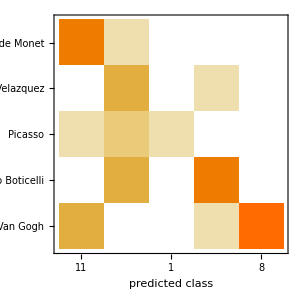

```mathematica
cmeasurements["Accuracy","Uncertainty"-> True]
cmeasurements["ConfusionMatrixPlot"]
```

It can be seen that the classifier confuses Vincent Van Gogh with Claude Monet, the most closely related styles from the five presented. This is ironic since Post-Impressionism was an opposing reaction to it’s predecessor movement, specially regarding the use of light an color in natural environments. The classifier and machine learning algorithms does not know this, but it may associate some of the recursive themes in both movements.

If we used the classifier function with van Gogh’s “The Yellow House” we would probably see Van Gogh and Claude Monet as the two most probable ones.

```mathematica
ReverseSort@cfunction[-Graphics-,"Probabilities"]
```

<|Claude Monet→0.337249,Vincent Van Gogh→0.210659,Sandro Boticelli→0.173232,Picasso→0.156082,Diego Velazquez→0.122779|>

We could apply the classifier function to any painting or image that is not in the training set. For instance classifying a picture of myself would result in the classification that associates to either Van Gogh, Diego Velazquez or Picasso depending on the training set.

```mathematica
ReverseSort@cfunction[-Graphics-,"Probabilities"]
```

<|Vincent Van Gogh→0.275685,Sandro Boticelli→0.222038,Diego Velazquez→0.212282,Claude Monet→0.14702,Picasso→0.142975|>

## Feature Extraction and Space Plot

Built-in functions that relate more to unsupervised learning can be used to see how paintings are separated depending on features extracted by different algorithms. For instance one could extract different features from a training set represented as a vector or finite list of values.

```mathematica
fextraction=FeatureExtraction[Keys@trainingset]
```

FeatureExtractorFunction[…]

Now we can apply this function to an image from the same set and see how the function generates a set of values in a large vector or list.

```mathematica
Keys@trainingset[[2]]
fextraction[%]
```

-Graphics-

{-1.36277,0.711688,-0.441452,-1.13776,0.633446,-2.03074,0.406146,-0.20666,0.930897,-0.901905,0.774058,0.693766,0.168342,-1.12062,0.00955031,-0.623124,-0.611897,-0.406199,1.43219,0.950967,0.147337,1.11005,0.462186,-1.41868,-0.753177,0.868333,-0.92447,-0.166048,-1.21014,-0.0356173,0.637229,-0.723301,-0.447528,0.0101236,-1.17267,0.8429,0.0737381,-1.46777,-1.77671,0.105535,-0.779721,0.0963864,0.497579,-0.793062,-1.24899,-1.01306,-0.547137,-0.178998,-1.86261,0.893659,-0.0187226,0.190848,1.36073,-0.944411,-0.860232,0.02617,0.978109,-0.284566,-1.76253,0.482626,0.541478,-0.895389,-0.317764,0.0906226,-0.953029,-2.60661,-3.37938,0.459535,-0.646405,-0.481725,-0.255179,-0.166098,-0.223941,-0.206394,0.953219,1.31871,-0.925413,0.120121,-0.762775,1.43231,-0.0518301,-0.228713,2.70215,-0.436819,0.164067,1.64551,1.2178,-1.26295,0.235107,0.528308,1.78726,-1.14127,1.28323,-0.426307,-1.3788,-1.92554,-1.49332,-0.0891027,0.505406,0.00503337,-0.613783,1.86242,0.673052,-0.370702,0.748667,-0.535272,0.028997,1.62325,0.325351,0.413481,0.168711,0.916384,-0.105755,0.945099,-0.86995,-1.20095,-1.73104,1.67642,-1.38863,-0.944041,1.01806,-0.581062,-0.657569,1.14749,0.805609,-1.08444,-0.846961,-0.333996,-1.43547,0.475416,-0.114968,0.336025,-0.977251,0.495026,-0.115468,1.91725,0.725033,-0.195825,0.364287}

We can also visualize this parametrization of the features in the images by a space plot.

```mathematica
FeatureSpacePlot[Keys@trainingset,ImageSize->Large,]
```

-Graphics-

As expected we can see groups of paintings from the same artist closer together. Alternatively, Impressionist paintings and landscapes can be seen to be on the opposite side and edge of those from portraits from the Baroque and Renaissance period.

To be able to see the different artists the feature Space Plot now will show points with a label of the first letter of the painter name.

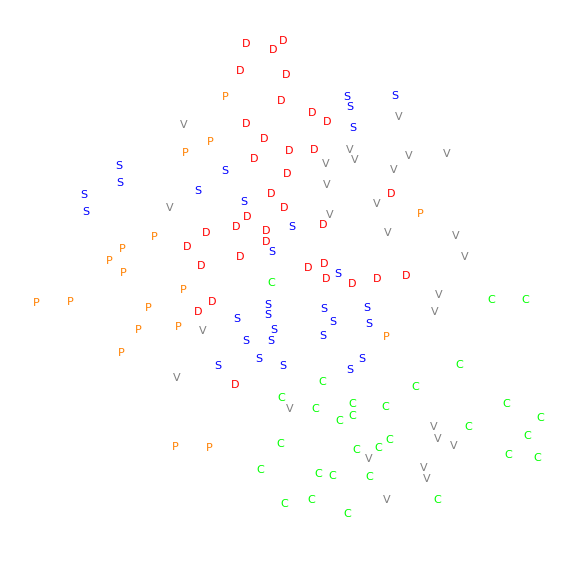

```mathematica
letterToColor=Thread[StringTake[#,{1}]&/@paintersList->colors];
g=FeatureSpacePlot[Keys[trainingset],];
g2=g/.
```

Similar to our first plot it can be seen how artists from the Baroque and the Renaissance are closer together in the plot, while Monet and Van Gogh are mixed together, again due to a similarity in style.

## Search

This code uses the feature extraction tools applied before to generate a function that, in this case, finds the image with the  nearest features. This could be thought of as the shortest distance between two vectors in a multidimensional space.

```mathematica
searchdataset=Keys@trainingset;
nearestf=FeatureNearest[searchdataset]
```

NearestFunction[…]

Again we can apply it to a picture of myself and see the resemblance.

```mathematica
First@nearestf[-Graphics-]
```

-Graphics-

Following the link, you could also upload an image of yourself or even one of your paintings, in the following API deployed to the cloud. You can see what painting from 5 of the most famous painters in history has the nearest features.

```mathematica
CloudDeploy[TestF=FormFunction[{"l"->"Image"},First@nearestf[#l]&]
]
```

CloudObject[https://www.wolframcloud.com/objects/6f88c14b-cc40-4b2b-9fb9-22eabf5b4bdb]

## Further explorations

Recent articles show studies of how machine learning algorithms differentiate between various styles of painting and movements in art history. It is quite interesting to understand how the algorithms differentiate and classify artworks. The tools in the Wolfram Language could be useful for this purpose.

https://arxiv.org/pdf/1801.07729.pdf

https://arxiv.org/abs/1706.07068

## Author contact information

Diego Gutierrez Coronel

06/28/2018

dgutie10@hawk.iit.edu

Special thanks to my mentor Vladimir Grankovsky